Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
Needs["MaTeX`"]
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=2 Pi c/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
```

```mathematica
lambdaInterpAu=Subdivide[Min[λAu],Max[λAu],3000];
nInterpFunction=Interpolation[Transpose[{λAu,nau}],Method->"Spline"];
kInterpFunction=Interpolation[Transpose[{λAu,kAu}],Method->"Spline"];
nInterpAu=nInterpFunction/@lambdaInterpAu;
kInterpAu=kInterpFunction/@lambdaInterpAu;
omegaAu=2 Pi c /lambdaInterpAu;
```

```mathematica
ϵ[ω_,ωp_,γ_]:=1-((ωp)^2/((ω)(ω+ I γ)))(*recibe en eV*)
```

```mathematica
alReal=Table[{ℏω,Re[Sqrt[ϵ[ℏω,13.142,0.197]]]},{ℏω,0.5,10,0.01}];
alImag=Table[{ℏω,Im[Sqrt[ϵ[ℏω,13.142,0.197]]]},{ℏω,0.5,10,0.01}];
```

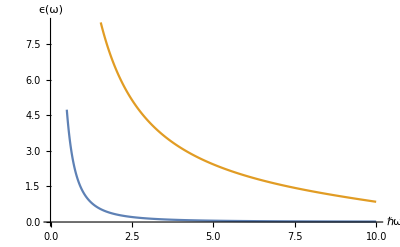

```mathematica
ListLinePlot[{alReal,alImag},AxesLabel->{"ℏω","ϵ(ω)"}]
```